```mathematica
Tau = 2 Pi;
Second[lst_]:=lst[[2]];
Exact[a_]:=Zeta[3]/(4 Tau a^3)//N;
```

```mathematica
ParallelPlates[a_,L_,n_,w_]:= Module[{t,s,r,d,G, V,idx,Rhs,P, Eqns,Vars, Sol},
Assert[a>0&&L>0&&n>1&&IntegerQ[n]];
If[w==0,Return[0]];
t[j_]:=j/n;
s[j_]:=(t[j-1]+t[j])/2;
r=L/n;
d[i_,j_]:=r (s[i]-s[j]);
idx=Floor[n/2];
G[i_,j_]:=w r/Tau  BesselK[1,w Sqrt[a^2 + d[i,j]^2]] / Sqrt[1 + (d[i,j]/a)^2]//N;
V[i_,j_]:=- 1/Tau BesselK[0, w Sqrt[a^2 + d[i,j]^2]]//N;
Rhs[0,i_]:=Sum[G[i,k]P[1,k], {k,1,n}];
Rhs[1,i_]:=Sum[G[i,k] P[0,k], {k,1,n}] + V[i,idx];
Eqns = Table[P[b,i]/2== Rhs[b,i], {b,0,1}, {i,1,n}]//Flatten;
Vars = Table[P[b,i],{b,0,1}, {i,1,n}]//Flatten;
Sol = NSolve[Eqns,Vars ];
P[0,idx]/.Sol//First
];

FullParallelPlates[a_,L_,n_,w_]:= Module[{t,s,r,d,idx,G,B,V,P},
Assert[a>0&&L>0&&n>1&&IntegerQ[n]];
If[w==0,Return[0]];

t[j_]:=j/n;
s[j_]:=(t[j-1]+t[j])/n;
r=L/n;
d[i_,j_]:=r (s[i]-s[j]);
G=Table[-w r/Tau  BesselK[1,w Sqrt[a^2 + d[i,j]^2]] / Sqrt[1 + (d[i,j]/a)^2]//N, {i, 1, n}, {j,1,n}];
B[di_]:=If[di==0,(1-Log[w/(2n)])/Tau,BesselK[0,w Abs[di]]/Tau] //N;
V=Table[
1/Tau BesselK[0, w Sqrt[a^2 + d[i,j]^2]]
(*+L/n Sum[G[[i,k]] B[d[k,j]],{k,1,n}]*)
//N,{i,1,n},{j,1,n}];
P =Inverse[IdentityMatrix[n] - G^2] G V;
r Table[P[[j,j]],{j,1,n}]
];

ParallelPlatesM[a_,L_,n_,w_]:= FullParallelPlates[a, L, n, w][[Floor[n/2]]];
IntegralParallelPlates[a_,L_,n_]:=Module[{pts,integrand,dx,ubound},
integrand[w_]:=If[w==0,0,w^2  ParallelPlates[a,L,n,w]];
ubound=6;
1/(L ) NIntegrate[integrand[w],{w,0,ubound},AccuracyGoal->3](*dx Sum[integrand[w],{w,dx/2,ubound-dx/2,dx}]*)
] ;
IntegralParallelPlates[a_,L_,n_,m_]:=Module[{pts,integrand,dx,ubound},
integrand[w_]:=w^2 ParallelPlates[a,L,n,w];
ubound=6;
dx=ubound/m;
dx Sum[integrand[w],{w,dx/2,ubound-dx/2,dx}]
];
```

```mathematica
TestCompare[IntegralParallelPlates[#, 1, 75]&,Exact, 1]
```

{Predicted: -0.048369,Exact: -0.0956566,0.505652}

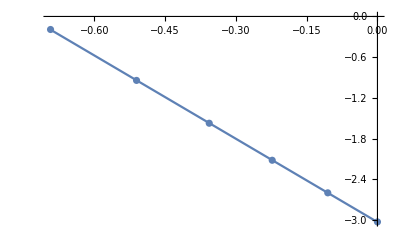
{-Graphics-,-4.09223,R^2 = 0.999995}

```mathematica
TestPowerDependency[IntegralParallelPlates[#,1,60]&,0.5, 1, 5]
```

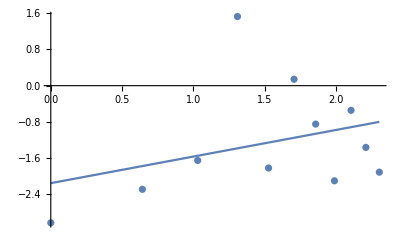
```mathematica
{-Graphics-,0.5873382692303601,"R^2 = 0.109933"}
```

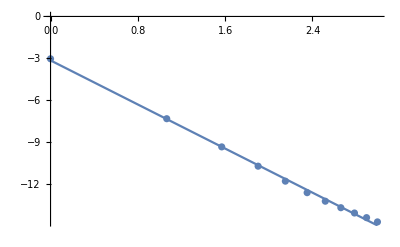
{-Graphics-,-3.94107,R^2 = 0.998429}

```mathematica
TestPowerDependency[IntegralParallelPlates[#,1,50]&,1, 20, 10]
```

```mathematica
Timing[IntegralParallelPlates[1, 1, 60]]
```

{12.5625,-0.0483679}

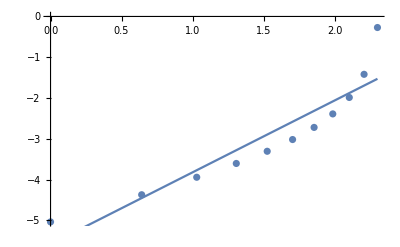
{-Graphics-,1.76147,R^2 = 0.854389}

```mathematica
TestPowerDependency[ParallelPlates[1,#,150,1]&,1,5, 10]
```

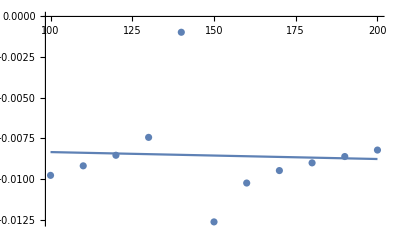
{-Graphics-,-4.26053×10^-6,R^2 = 0.00245471}

```mathematica
TestLinearDependency[ParallelPlates[1,#,75,1]&,100,200, 10]
```

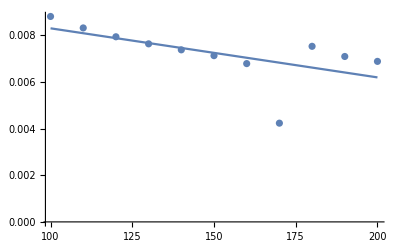
{-Graphics-,-0.0000210468,R^2 = 0.353742}

```mathematica
TestLinearDependency[ParallelPlates[1,#,120,1]&,100,200, 10]
```

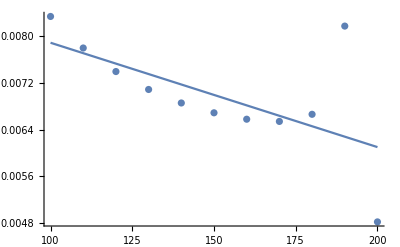
{-Graphics-,-0.0000178927,R^2 = 0.376159}

```mathematica
TestLinearDependency[ParallelPlates[1,#,120,1]&,100,200, 10]
```

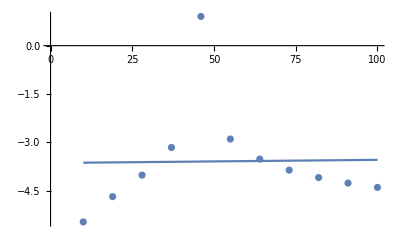
{-Graphics-,0.000986479,R^2 = 0.00031906}

```mathematica
TestLogarithmicDependency[ParallelPlates[2,#,75,1]&,10, 100,10]
```

```mathematica
pts = Table[ParallelPlates[2, L, 75, 1], {L, {0.125, 0.25, 0.5, 1, 2, 4, 8}}]
```

{-0.0000504389,-0.00010088,-0.000201779,-0.000403704,-0.000808583,-0.00162663,-0.0033312}